## NONLINEAR TEST CODE

This quits the kernal

```mathematica
Quit[]
```

Below tests whether or not the function that solves dy/dt=c y|y|^2+d y|y|^4 is working correctly
After comparing with my solution, going from 0 to 1 with a step size of 0.01 gives 1.6*10^-6 %error. 
With a step size of 0.1 we get a 4*10^-5% error
with 0.001 step size we get a 1.6*10^-6% error

```mathematica
c=0.1+0.4I;
d=-0.1+0.1I;
y0 = 1;
maxtime = 1;

f1[y_] = c*y*Abs[y]^2+d*y*Abs[y]^4;
s=NDSolve[{y'[x]==f1[y[x]],y[0]==y0},y,{x,0,maxtime}];
y[maxtime]/.s
(*Plot[Im[Evaluate[y[x]/.s]],{x,0,1},PlotRange->All]*)
```

{0.877583+0.479426 ⅈ}

The Percentage Error Calculation:

```mathematica
value = (0.877582802529+0.479425192098I)
100*Abs[(0.8775825529111512+0.4794255516237757 ⅈ) - value]/Abs[0.8775825529111512+0.4794255516237757 ⅈ]
```

0.877583+0.479425 ⅈ

0.0000437685

## LINEAR TEST CODE

This quits the kernal

```mathematica
Quit[]
```

Below tests whether or not the function that solves dψ/dt=a ψ+b ∇^2 ψ is working correctly.

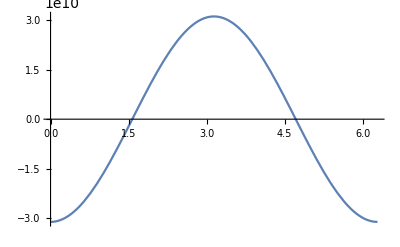

```mathematica
a=3+0.5I;
b=0.5-I;
y0[x_] = Sin[Pi Cos[x]]; 


maxtime = 10; (*This is because in python I insist on an array with the correct size, which includes the input function*)

boxsize = 2π;
Xstepsize=0.001;

sol=NDSolve[{D[u[t,x],t]==a*u[t,x]+b*D[u[t,x],{x,2}],u[0,x]==y0[x],u[t,0]==u[t,boxsize]},u,{t,0,maxtime},{x,0,boxsize}][[1]];

Plot[Re[Evaluate[u[maxtime,x]/.sol]],{x,0,boxsize},PlotRange->All]


xarr = Range[0,boxsize,Xstepsize];
finalFunct[x_]={Re[Evaluate[u[maxtime,x]/.sol]],Im[Evaluate[u[maxtime,x]/.sol]]};
finalArr = Map[finalFunct,xarr];
location = NotebookDirectory[]<>"testlinear.csv";
Export[location,finalArr];
```

When comparing the python code to the mathematica code, we get a 0.06% error when we take the xstep to be 0.001.
If we make the xstep larger, however, we get a significantly larger error. (xstep = 0.01 gives a maximum error of 147%).
more interestingly, with xstep = 0.002, we get %error = 0.06%, but with xstep = 0.003 we get %error = 147%
Time didn’t have a big role, and given that a 0.01 step size gives 0.5% error, and we have better than this here, we should be fine. 

Note: %error is defined with Max[Abs[python-mathematica]/Max[Abs[python]]]*100
This is because, if I was to calculate %error pointwise, if the function is near zero, the %error will be large since you divide by a number near zero. Incidently, when calculating the %error this way, the maximum error occurs at the maximuma/minima of the function. % error for time is actually better than this!



After 10s, we get an error of 0.28% with dx=0.001